```mathematica
Dynamic[Refresh[data=Import["D:\\FING\\Tesis\\AGIO\\bin\\epochs.csv"];
data = Drop[Transpose[Drop[data,1]],1];
randBaseline = Mean[data[[4]]];
greedyBaseline = Mean[data[[5]]];
Show[ListLinePlot[{data[[1]],data[[2]],data[[3]]}],Plot[randBaseline,{x,0,Length[data[[1]]]}]],UpdateInterval->5]]
Dynamic[N[greedyBaseline]]
Dynamic[N[randBaseline]]
```

solo angulos

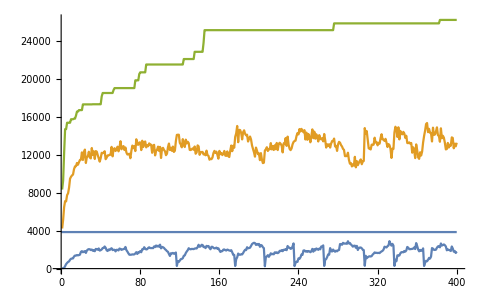

solo celdas

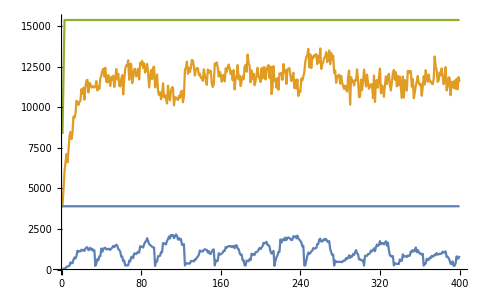

todas las entradas